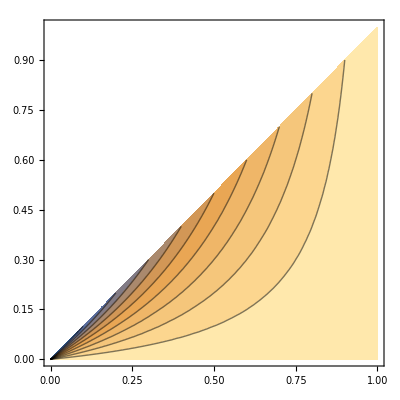

```mathematica
ContourPlot[1+λ (ρ-1)/ρ, {ρ, 0, 1}, {λ, 0, 1}, RegionFunction->Function[{ρ,λ,z},ρ>λ], PlotRange->{0, 1}]
```

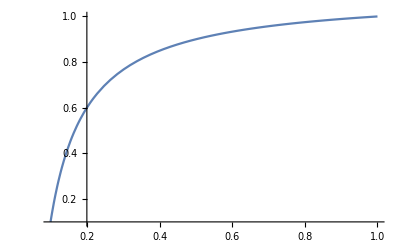

```mathematica
λ = 0.1;
Plot[1+λ (ρ-1)/ρ, {ρ, λ, 1}, PlotRange->All]
```

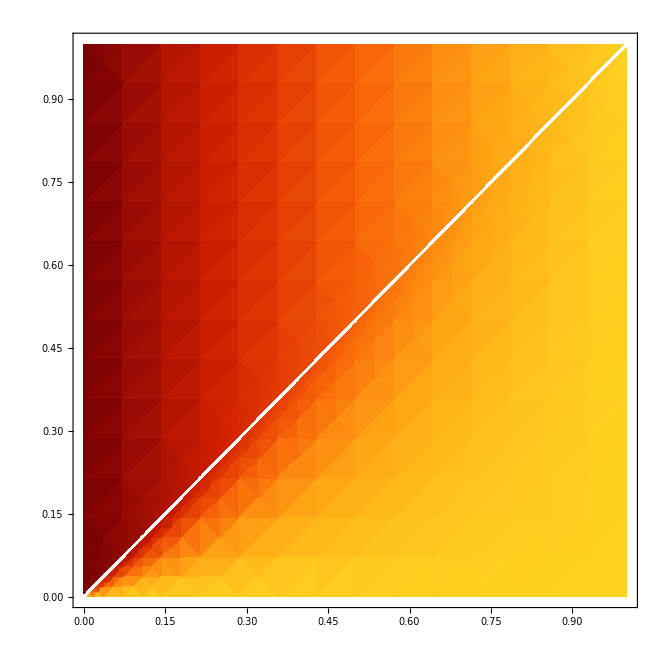

```mathematica
f[ρ_, λ_] := Piecewise[{{1+(λ(ρ-1))/ρ, ρ>λ}}, ρ];
DensityPlot[f[ρ, λ], {ρ, 0, 1}, {λ, 0, 1}, ColorFunction->"SolarColors"]
```